8.1 Use RegularPolygon to draw a triangle.



```mathematica
Graphics[RegularPolygon[3]]
```

8.2 Make graphics of a red circle.

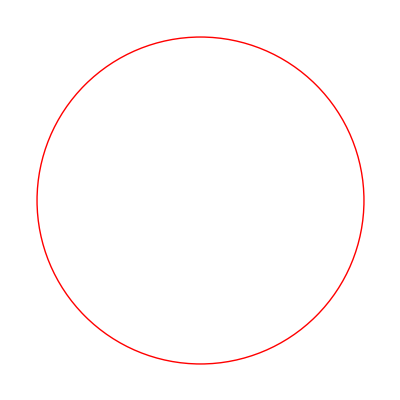

```mathematica
Graphics[Style[Circle[], Red]]
```

8.3 Make a red octagon.

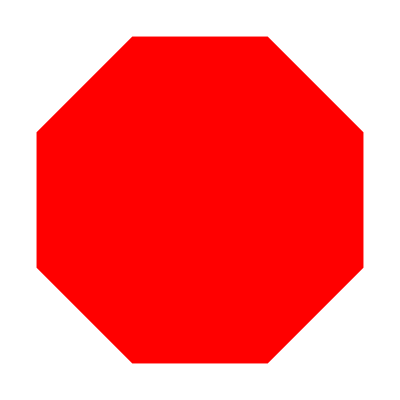

```mathematica
Graphics[Style[RegularPolygon[8], Red]]
```

8.4 Make a list of disks with hue varying from 0 to 1 in steps of 0.1.


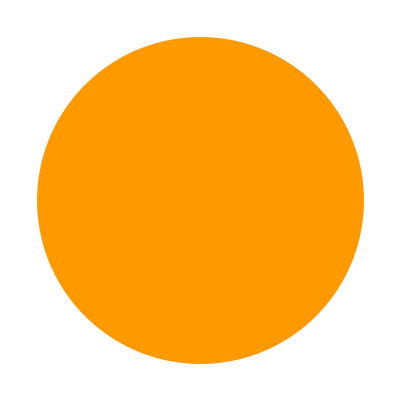
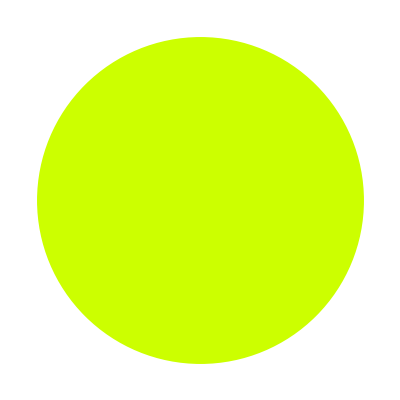
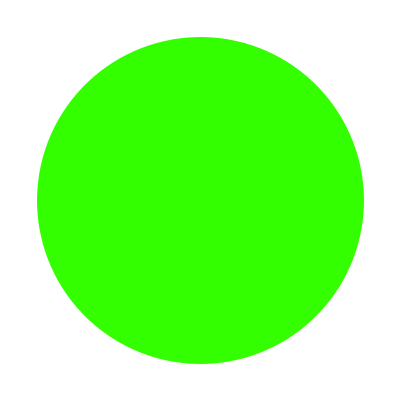
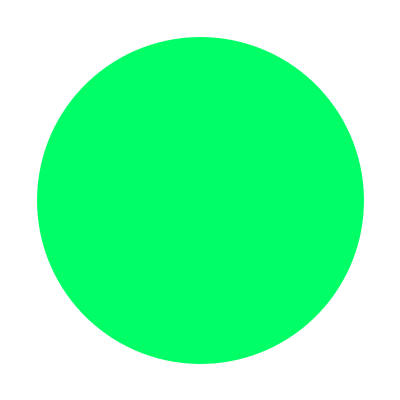
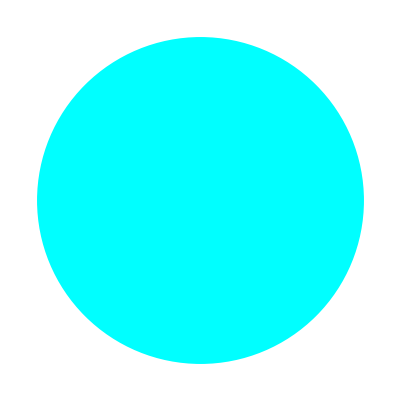
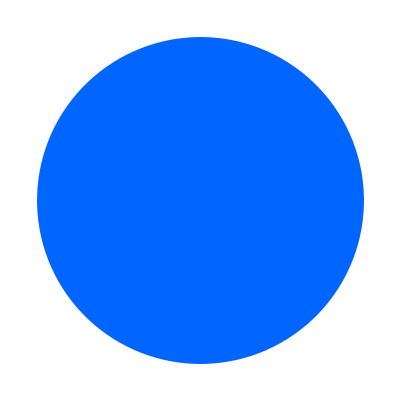
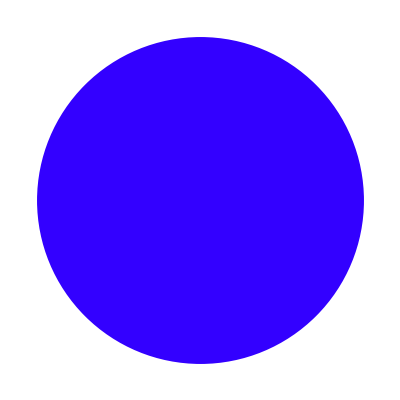
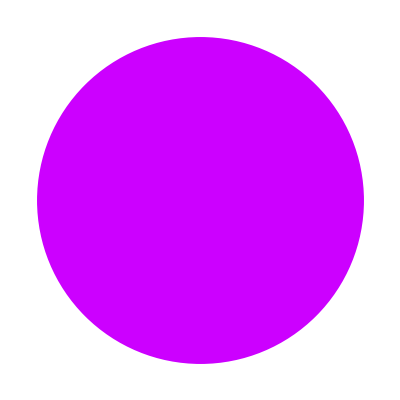
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[Disk[], Hue[x]]], {x, 0, 1, 0.1}]
```

8.5 Make a column of a red and green triangle.

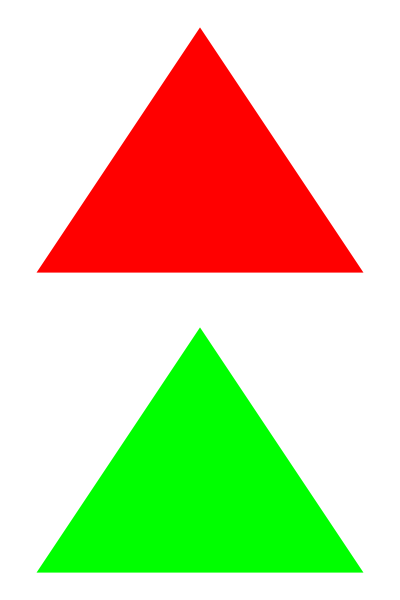

```mathematica
Column[{Graphics[Style[RegularPolygon[3], Red]], Graphics[Style[RegularPolygon[3], Green]]}]
```

8.6 Make a list of pink regular polygons with between 5 and 10 sides.

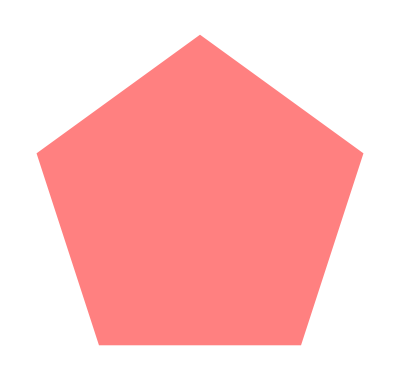
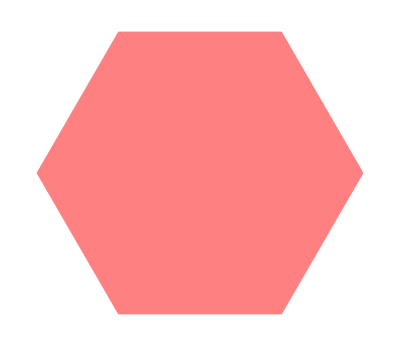
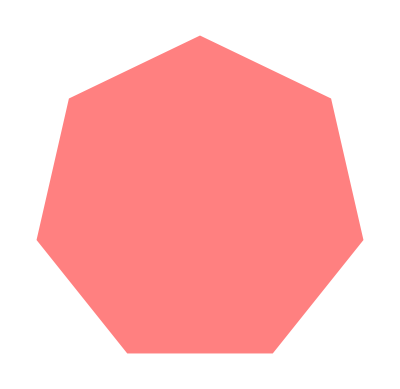
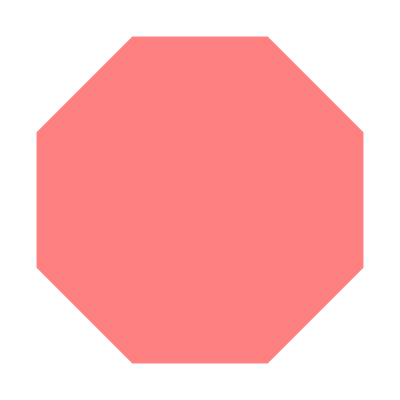
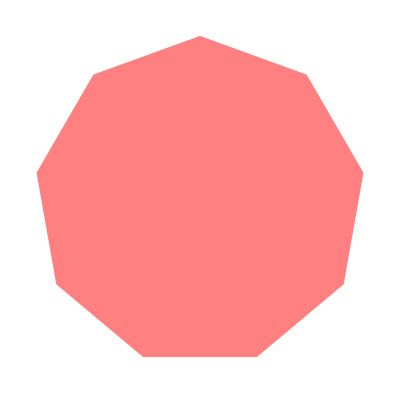
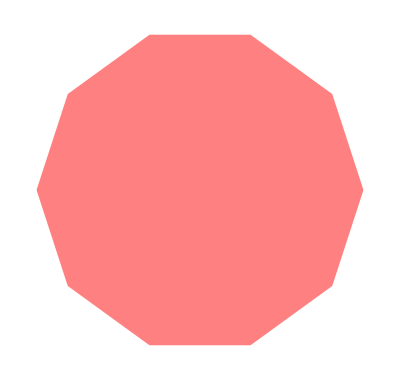

```mathematica
Table[Graphics[Style[RegularPolygon[sides], Pink]], {sides, 5, 10}]
```

8.7 Make a graphic of a purple cylinder.

```mathematica
Graphics3D[Style[Cylinder[], Purple]]
```

-Graphics3D-

8.8 Make a list of randomly colored polygons with 8 down to 3 sides, and apply Graphics to the list to show them all overlaid.

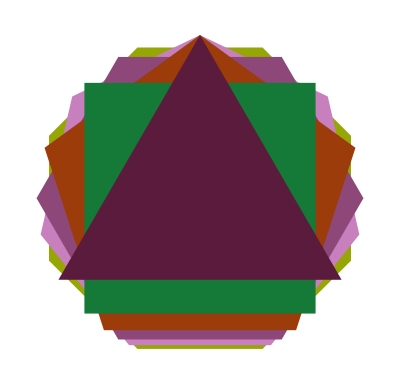

```mathematica
Graphics[Table[Style[RegularPolygon[sides],RandomColor[]], {sides, 8, 3, -1}]]
```